# A 3D Virtualization of Atom Interferometry

What’s the underlying mechanism of the world’s most precise atomic clock

Wangping Ren, June 26,  2019

From Thomas Young’s double-slit experiment to the observation of gravitational waves by LIGO, interference patten is widely observed and applied in various fields. In atomic physics, atom interferometry is commonly used to determine the transition frequency between quantum states within atoms. For example, the Ramsey’s interferometry is used in one of the world’s most precise Cesium atomic clock located at NIST where the current frequency standard corresponds to the energy difference between two spin states of an isolated Cesium-133 atom.

## How earthquakes are created?

There is no clear model for earthquake mechanism. However, just by looking at how earthquakes are spatially distributed, one can deduce a rough mechanism.

Earthquake spatial distribution of magnitude 6 or higher from 1900 till now, with black lines, showing the large globe plate boundaries:

```mathematica
p1 = GeoGraphics[ResourceData["Large Global Plate Boundaries"][All,"Polygon"]];
p2 = GeoHistogram[EarthquakeData[All, 6,{{1900,1,1},Now},"Position"],200, ColorFunction->"SolarColors", PlotLegends->Automatic];
Show[p1,p2]
```

-Graphics-

As depicted, most of earthquakes occur near the plate boundaries, showing the most susceptible regions.  For this reason, it is believed that stick-slip of sheared plates and crack propagation are main phenomena involved in earthquakes.

## How much energy is dissipated?

The earthquake magnitude is not a clear indicator of the energy. A useful empirical law  [Bath, 1966] relates the magnitude and energy as follows. The energy produced by earthquakes fluctuates in time, but remains almost of the same order of magnitude in large enough time windows.

Monthly released energy by earthquakes on the glob, within the year 2006:

```mathematica
Energy[M_] := 10^(5.24+1.44*M);
monthlyenergy[i_] := Total[Energy/@EarthquakeData[All,All,{{2006,i,1},{2006,i,31}}, "Magnitude"]["Values"]];
ListLinePlot[Table[monthlyenergy[i], {i,12}]]
```

-Graphics-

A crucial question is how the produced power by earthquakes compares with other powers such as heat flux to the surface. Using the magnitude-energy  relation, we can calculate total power created by earthquakes.

Power created by all earthquakes within year 2006:

```mathematica
earthquakesM = EarthquakeData[All,All,{{2006,1,1},{2007,1,1}}, "Magnitude"]["Values"];
earthquakesPower = Quantity[Total[Energy/@earthquakesM],"joules"]/UnitConvert[1"year","seconds"]
```

4.66324×10^9 J/s

The power is four orders of magnitude smaller than the total heat flow from the earth interior, 47 terawatts. This can be also due to incompleteness of the dataset.

## How earthquakes are distributed?

Gutenberg and Richter have showed that earthquakes energy distribution follows a power-law for a wide range of magnitudes. As magnitude of earthquakes relate to logarithm of their energy, this law can be shown easily using magnitudes.

Distribution of number of earthquakes in California between years 1980 to 1990:

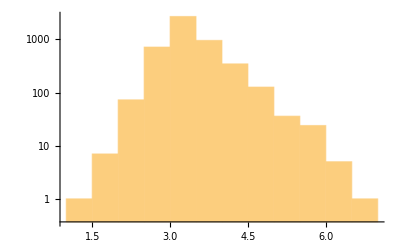

```mathematica
earthquakesM=EarthquakeData[Entity["AdministrativeDivision",{"California","UnitedStates"}],All,{{1980,1,1},{1990,1,1}},"Magnitude"]["Values"];
Histogram[earthquakesM, 15, ScalingFunctions->"Log"]
```

Many believe the value of the exponent of this power - law is crucial to calculate, as it shows the universality class of the underlying physical phenomena.

Finding the exponent of power law by fitting a line in above diagram from the maximum to the end, by converting to energy:

```mathematica
MagnitudePDF = HistogramList[earthquakesM, 15];
maxpos = Ordering[MagnitudePDF[[2]],-1][[1]];
clearedPDF = Drop[#,maxpos-1]&/@ MagnitudePDF;
data = Transpose[{BlockMap[Mean, clearedPDF[[1]],2,1],Log10[clearedPDF[[2]]]}];
Coefficient[Fit[data,{1,x},x],x,1]/1.44
```

-0.652549

The exponent, which is about 2/3, is far from many theoretical predictions with exponent 1.5.  This exponent may change in different time or spatial windows.

## Further explorations

Earthquake statistics has been further explored extensively. One important problem is how earthquakes are correlated with past or future ones. Declustering of earthquakes, such as aftershocks, mainshocks or foreshocks, can be investigated using wide variety of definitions. Moreover, the more detailed spatial distribution such as depth can be added for further explorations of the data.

The methods here can be extended to many other similar systems, which can be described as a time series with erratic intermittent behavior like earthquake shocks. Similar systems include granular materials, crack propagation, and crackling noise.

## Author contact information

agheal@gmail.com